```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Define the states*)
x = {m1,m2,cme,e1,e2,cep,p1};
```

```mathematica
(*Define the ode*)
fm1=-k1*m1+k2*m2;
fm2 =k1*m1-k2*m2-k3on*m2*e1+(k3off+k4)*cme;
fcme =k3on*m2*e1-(k3off+k4)*cme;
fe1=-k3on*m2*e1+k3off*cme+k6*cep;
fe2=k4*cme-k5on*p1*e2+k5off*cep;
fcep =-k6*cep+k5on*p1*e2-k5off*cep;
fp1=k6*cep-k5on*p1*e2+k5off*cep;
f ={fm1,fm2,fcme,fe1,fe2,fcep,fp1};
```

```mathematica
(*Reduce system by applying conservation laws*)
g1=m1+m2+cme-mtot;
g2=e1+e2+cep+cme-etot;
g3=p1+cep-ptot;
g= {g1,g2,g3};
sol=Solve[g == 0, {m1,e1,p1}];
m1=Part[sol,1,1,2];
e1=Part[sol,1,2,2];
p1=Part[sol,1,3,2];
```

```mathematica
(*fR = Reduced ODE*)
fR = f[[{2,3,5,6}]];
fR//MatrixForm;
```

Define the Parameter trafo try 1: 
Add b*cep to e2

```mathematica
M=DiagonalMatrix[Table[1,4]];
M[[1,2]]=a;
M[[3,2]]=0;
M[[3,4]]=1;
xP=Table[ToExpression[StringJoin[ToString[{m2,cme,e2,cep}[[i]]],"P"]],{i,4}];
myrules = Table[{m2,cme,e2,cep}[[i]]-> ((Inverse[M].xP)[[i]]),{i,4}];
```

```mathematica
M//MatrixForm
(*Apply the Trafo*)
fRP = fR/.myrules;
fRP = M.fRP;
```

(1 | a | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 1
0 | 0 | 0 | 1)

```mathematica
(*FullSimplify[fRP/.{a->0.5, b->1}]//MatrixForm;*)
```

Reduce the system by kicking out cmeP and cepP via QSS;

```mathematica
sol4=Solve[{fRP[[2]] ==0, fRP[[4]]==0},{ cmeP, cepP}];
cmeP = Part[sol4,1,1,2];
cepP=Part[sol4,1,2,2];
```

```mathematica
FullSimplify[Simplify[fRP[[1]]/.a->k1/(k1+k2)]]//InputForm
```

-((k1 + k2)*m2P) + k1*mtot

```mathematica
Simplify[fRP[[1]]/.a->k1/(k1+k2)]
```

```mathematica
-k2 m2P+k1 (-m2P+mtot)
```

```mathematica
detot =D[fRP[[1]],ptot];
```

```mathematica
Simplify[detot]
```

-((e2P ((-1+a) k1+a k2) k5on (-k3off k5off+a e2P k3on k5off-a etot k3on k5off-k4 k5off-e2P k3off k5on+a e2P^2 k3on k5on-a e2P etot k3on k5on-e2P k4 k5on-k3off k6+a e2P k3on k6-a etot k3on k6-k4 k6+k3on k5off m2P+e2P k3on k5on m2P+k3on k6 m2P+a e2P k3on k5on ptot+√(4 a k3on^2 (k5off+e2P k5on+k6) m2P (e2P^2 k5on-etot (k5off+k6)+e2P (k5off-etot k5on+k6+k5on ptot))+(k3off (k5off+e2P k5on+k6)+(k5off+e2P k5on+k6) (k4+k3on m2P)-a k3on (e2P^2 k5on-etot (k5off+k6)+e2P (k5off-etot k5on+k6+k5on ptot)))^2)))/(2 (k5off+e2P k5on+k6) √(4 a k3on^2 (k5off+e2P k5on+k6) m2P (e2P^2 k5on-etot (k5off+k6)+e2P (k5off-etot k5on+k6+k5on ptot))+(k3off (k5off+e2P k5on+k6)+(k5off+e2P k5on+k6) (k4+k3on m2P)-a k3on (e2P^2 k5on-etot (k5off+k6)+e2P (k5off-etot k5on+k6+k5on ptot)))^2)))

```mathematica
Solve[detot == 0,a]
```

{{a→k1/(k1+k2)}}

```mathematica
k1=0.1;
k2 = 0.1;
k3on=0.01;
k3off=1;
k4=1;
k5on=0.01;
k5off=1;
mtot=100;
ptot=100;
etot=1000;
```

```mathematica
(*FullSimplify[detot];*)
```

```mathematica
plotfun[a2_]:=Simplify[detot/.{a->0.5, m2P ->20, e2P -> 800}] (*These are approk4mate steady state values*)
```

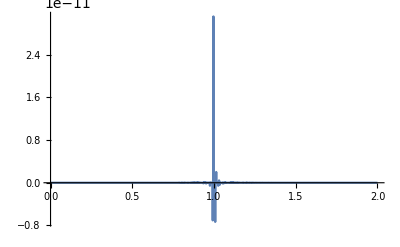

```mathematica
Plot[plotfun[a2],{a2,0,2}, PlotRange->Full] (* Doesn't have a root*)
```

```mathematica
Solve[detot == 0,a]
```

```mathematica
{{a->k1/(k1+k2)}}
```

Derive cmeP with respect to ptot, while setting b=1.

```mathematica
dptot =D[fRP[[1]],ptot];
```

```mathematica
(*FullSimplify[dptot]*)
```

```mathematica
FullSimplify[dptot/.{b->1}]
```

0

```mathematica
FullSimplify[fRP/.{a->1, b->1}]
```

```mathematica
{1/(2 k3on)(k2 k3off-k2 e2P k3on+k2 etot k3on-2 k1 k3on m2P-k2 k3on m2P+2 k1 k3on mtot+k2 k4-k2 √(4 (e2P-etot) k3on^2 m2P+(k3off+k3on (-e2P+etot+m2P)+k4)^2)),0,1/2 (-(k6 (k6+e2P k5on+k5off+k5on ptot-√(-4 e2P k5on^2 ptot+(k6+k5off+k5on (e2P+ptot))^2)))/k5on+1/k3on k4 (k3off-e2P k3on+etot k3on+k3on m2P+k4-√(4 (e2P-etot) k3on^2 m2P+(k3off+k3on (-e2P+etot+m2P)+k4)^2))),0}
```

```mathematica
FullSimplify[fRP/.{a->k1/(k1+k2), b->1}]
```

```mathematica
{-(k1+k2) m2P+k1 mtot,0,1/2 (-(k6 (k6+e2P k5on+k5off+k5on ptot-√(-4 e2P k5on^2 ptot+(k6+k5off+k5on (e2P+ptot))^2)))/k5on+1/(k1 k3on)(k1+k2) k4 (k3off-(k1 e2P k3on)/(k1+k2)+(k1 etot k3on)/(k1+k2)+k3on m2P+k4-√(1/(k1+k2)^2(4 k1 (k1+k2) (e2P-etot) k3on^2 m2P+(k2 (k3off+k3on m2P+k4)+k1 (k3off+k3on (-e2P+etot+m2P)+k4))^2)))),0}
```